```mathematica
S[ϵ_,nmax_]:=Sum[a[n]*ϵ^n,{n,1,nmax}]+O[ϵ]^(nmax+1)
Sk[ϵ_,nmax_,k_]:=S[ϵ,nmax]^k
xqm1[ϵ_,b_,q_,nmax_,kmax_]:= Sum[Binomial[q-1,k]/k!*b^(q-1-k)*Sk[ϵ,nmax,k],{k,0,kmax}]
```

```mathematica
q=1/2;
kmx=3;(*outter sum max index*)
nmx=3; (*inner sum max index*)

polyR=Simplify[xqm1[ϵ,b,q,nmx,kmx]];
coefsR=CoefficientList[polyR,ϵ];
polyL = S[ϵ,Length[cflright] - 1];
coefsL=CoefficientList[polyL,ϵ];
(*Collect[polyL+polyR,ϵ] *)
Thread[Equal[coefsL,coefsR]]



(*
tot = Total[Table[a[n],{n,1,Length[cflright] - 1}]/.cf[[1]]];
x[bee_,que_,lam_]:=tot/.{b->bee,q->que,λ->lam}*)
```

{0==1/(√b),a[1]==-a[1]/(2 b^(3/2)),a[2]==(3 a[1]^2-8 b a[2])/(16 b^(5/2)),a[3]==(-5 a[1]^3+36 b a[1] a[2]-48 b^2 a[3])/(96 b^(7/2))}

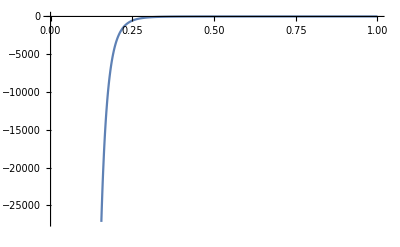

-10.5197

```mathematica
Plot[x[b,0.5,1],{b,0,1}]
```

```mathematica
cflright
cflleft
```

{0,b^(-1+q) q λ,b^(-2+q) (-1+q) q λ a[1],1/4 b^(-3+q) (-1+q) q λ ((-2+q) a[1]^2+4 b a[2]),1/36 b^(-4+q) (-1+q) q λ ((6-5 q+q^2) a[1]^3+18 b (-2+q) a[1] a[2]+36 b^2 a[3]),1/576 b^(-5+q) (-1+q) q λ ((-24+26 q-9 q^2+q^3) a[1]^4+48 b (6-5 q+q^2) a[1]^2 a[2]+288 b^2 (-2+q) a[1] a[3]+144 b^2 ((-2+q) a[2]^2+4 b a[4])),1/14400 b^(-6+q) (-1+q) q λ ((120-154 q+71 q^2-14 q^3+q^4) a[1]^5+100 b (-24+26 q-9 q^2+q^3) a[1]^3 a[2]+1200 b^2 (6-5 q+q^2) a[1]^2 a[3]+1200 b^2 (-2+q) a[1] ((-3+q) a[2]^2+6 b a[4])+7200 b^3 ((-2+q) a[2] a[3]+2 b a[5]))}

{0,a[1],a[2],a[3],a[4],a[5],a[6]}